# FIR Filters

## Testy w Mathematica

```mathematica
a
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Length@a
```

1023

32

63

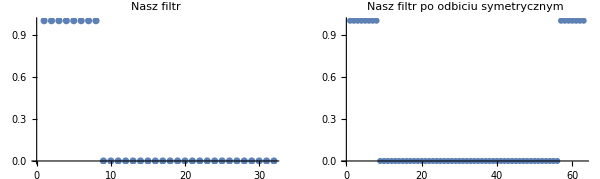

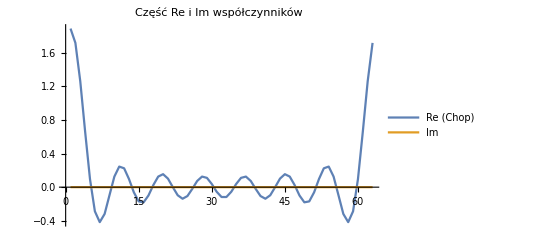

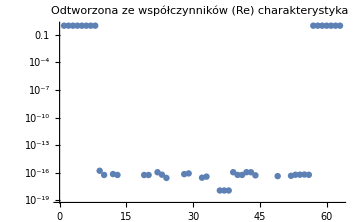

```mathematica
dx=1/(31);
FilterFunc[x_]:=UnitStep[-x+1/4];
b=Table[FilterFunc[x],{x,0,1,dx}];
Length@b
a=Join[b,Conjugate[Reverse[Drop[b,1]]]];
Length@a
GraphicsRow[{ ListPlot[b,PlotLabel->"Nasz filtr"],ListPlot[a,PlotLabel->"Nasz filtr po odbiciu symetrycznym"]},ImageSize->600]
ListLinePlot[{Chop@Fourier@a,Im@Fourier@a},PlotRange->Full,PlotLabel->"Część Re i Im współczynników",PlotLegends->{"Re (Chop)","Im"}]
ListLogPlot[InverseFourier@Chop@Fourier@a, PlotLabel->"Odtworzona ze współczynników (Re) charakterystyka",ImageSize->Medium]
```

```mathematica
FilterFunc[x_]:=UnitStep[-x+1/4];(*N[UnitStep[x-7/8]+0.5*UnitStep[x-3.5/8]*UnitStep[-x+4.5/8]];*)(*Exp[-1000(x-0.2)^2];*)
Manipulate[
fparams={1, -1}; (*params for DSP*)
n=512;dx=1./(n-1);
(*a=Table[UnitStep[-x+1/4],{x,0,1,dx}];*)
(*a=Table[If[x≤1/2,Exp[-100x^2],Exp[-100(1-x)^2]],{x,0,1,dx}];*)
b=Table[FilterFunc[x],{x,0,1,dx}];
a=Join[b,Conjugate[Reverse[Drop[b,1]]]];
siga=Table[Sin[1u(x)],{x,0,1,dx}];
sigb=Table[Sin[2u (x)],{x,0,1,dx}];
sigc=Table[Sin[8u (x)],{x,0,1,dx}];
coefMathInv=InverseFourier[a, FourierParameters->fparams];
coefMath=Fourier[coefMathInv, FourierParameters->fparams][[1;;n]];
filteredA=Chop@ListConvolve[coefMathInv[[1;;n/2]],siga];
filteredB=Chop@ListConvolve[coefMathInv[[1;;n/2]],sigb];
filteredC=Chop@ListConvolve[coefMathInv[[1;;n/2]],sigc];
{{ListPlot[a,Filling->Axis, ImageSize->Medium, PlotRange->All],
ListPlot[{siga,sigb,sigc},Filling->Axis,PlotLegends->{"1x","2x","8x"}, PlotRange->{{0,n},{-1,1}},ImageSize->Medium]},{ListPlot[{Chop@coefMath},Filling->Axis, ImageSize->Medium, PlotRange->All,PlotLabel->"Fourier"],
ListPlot[{Chop@coefMathInv},Filling->Axis, ImageSize->Medium, PlotRange->All,PlotLabel->"Inverse Fourier"],
ListPlot[{filteredA,filteredB,filteredC}, PlotRange->{{0,n},{-1,1}},Filling->Axis,ImageSize->Medium,PlotLegends->{"1x","2x","8x"}]}}
,{{u,8,"mulitplier"},8,100},SynchronousUpdating->False]
```

1/32

{1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1}

{17.+0. ⅈ,15.1566+1.38778×10^-16 ⅈ,10.334-4.16334×10^-16 ⅈ,4.33379+2.01228×10^-16 ⅈ,-0.752051-6.66134×10^-16 ⅈ,-3.43891+4.16334×10^-16 ⅈ,-3.41478-2.77556×10^-17 ⅈ,-1.52741-1.66533×10^-16 ⅈ,0.758286+8.32667×10^-16 ⅈ,2.12725-2.77556×10^-16 ⅈ,2.01199-3.88578×10^-16 ⅈ,0.743836+0. ⅈ,-0.768963+2.22045×10^-16 ⅈ,-1.61803+0. ⅈ,-1.3957+1.11759×10^-15 ⅈ,-0.360892-9.76225×10^-17 ⅈ,0.784543-1.55155×10^-16 ⅈ,1.34613-2.92992×10^-17 ⅈ,1.03959+1.97166×10^-16 ⅈ,0.121466-1.01672×10^-16 ⅈ,-0.805754+2.02443×10^-17 ⅈ,-1.17686+6.54714×10^-18 ⅈ,-0.799241-3.91795×10^-16 ⅈ,0.0538955+2.44661×10^-16 ⅈ,0.833685-1.74101×10^-16 ⅈ,1.0617+3.16869×10^-16 ⅈ,0.618034+0. ⅈ,-0.199121+1.84623×10^-17 ⅈ,-0.869963+3.05789×10^-16 ⅈ,-0.978848-3.07316×10^-16 ⅈ,-0.468136-1.0984×10^-16 ⅈ,0.332782+1.07204×10^-16 ⅈ,0.91706+1.1555×10^-16 ⅈ,0.91706+5.35228×10^-16 ⅈ,0.332782+1.39509×10^-16 ⅈ,-0.468136+2.26832×10^-16 ⅈ,-0.978848+3.11485×10^-16 ⅈ,-0.869963-5.09283×10^-16 ⅈ,-0.199121-4.27891×10^-16 ⅈ,0.618034+0. ⅈ,1.0617-1.80946×10^-16 ⅈ,0.833685+3.05789×10^-16 ⅈ,0.0538955+5.93016×10^-17 ⅈ,-0.799241+7.05267×10^-17 ⅈ,-1.17686-2.84339×10^-16 ⅈ,-0.805754+1.1555×10^-16 ⅈ,0.121466+3.54862×10^-16 ⅈ,1.03959+2.50981×10^-16 ⅈ,1.34613+9.81359×10^-17 ⅈ,0.784543-5.51326×10^-17 ⅈ,-0.360892+1.27757×10^-17 ⅈ,-1.3957-4.27891×10^-16 ⅈ,-1.61803+0. ⅈ,-0.768963-1.09388×10^-15 ⅈ,0.743836-9.76225×10^-17 ⅈ,2.01199+2.01942×10^-16 ⅈ,2.12725+7.34746×10^-16 ⅈ,0.758286-4.36365×10^-16 ⅈ,-1.52741-1.01672×10^-16 ⅈ,-3.41478-7.43801×10^-16 ⅈ,-3.43891-1.2297×10^-15 ⅈ,-0.752051+3.44383×10^-16 ⅈ,4.33379-1.12435×10^-16 ⅈ,10.334+6.70607×10^-16 ⅈ,15.1566+3.16869×10^-16 ⅈ}

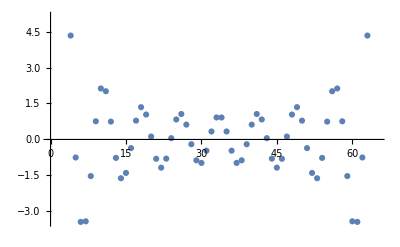

```mathematica
dx=1/32
FilterFunc[x_]:=UnitStep[-x+1/4];
b=Table[FilterFunc[x],{x,0,1,dx}];
a=Join[b,Conjugate[Reverse[Drop[b,1]]]]
c=Fourier[a, FourierParameters->{1,-1}]
ListPlot@Chop[c]
```

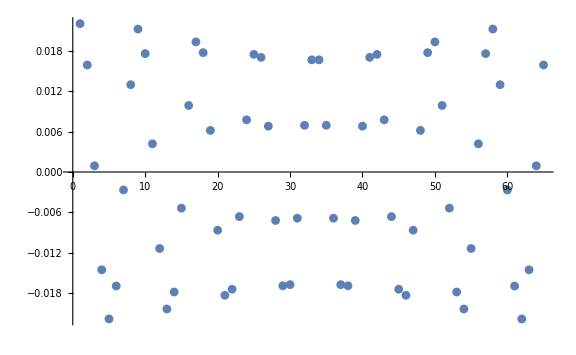

```mathematica
ListPlot[Chop@c-Chop@Fourier[{1,1,1,1,1,1,1,0.999,0.99,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.99,0.999,1,1,1,1,1,1},FourierParameters->{1,-1}],ImageSize->Large ]
```

### Odtwarzanie transmitancji

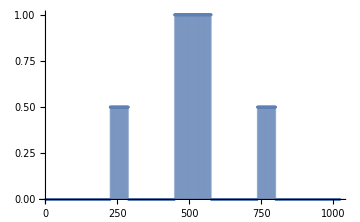

```mathematica
ListPlot[Chop@Fourier[InverseFourier[a, FourierParameters->fparams], FourierParameters->fparams],PlotRange->Full,ImageSize->Medium, Filling->Axis]
```

## Wyniki z C

```mathematica
ImportComplex[name_]:=Import[name,"Data"][[All,3]]+ⅈ Import[name,"Data"][[All,4]];
```

### Porównanie współczynników double i fixed point w C

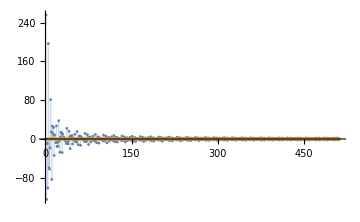
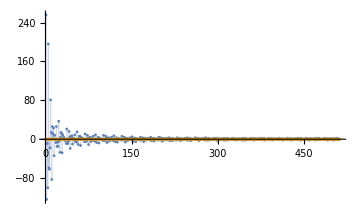

```mathematica
coefs=ImportComplex["coefs.dat"];
coefsReal=ImportComplex["coefsReal.dat"];
{ListPlot[{Re@coefs,Im@coefs},PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListPlot[{Re@coefsReal,Im@coefsReal},PlotRange->Full, Filling->Axis,ImageSize->Medium]}
```

#### Różnica pomiędzy współczynnikami double i fixed point w C

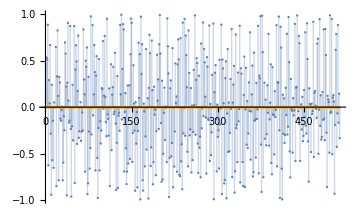

```mathematica
ListPlot[{Re@coefsReal-Re@coefs,Im@coefsReal-Im@coefs},PlotRange->Full, Filling->Axis,ImageSize->Medium]
```

#### Różnica między współczynnikami double i z Mathematica

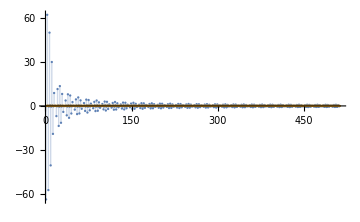

```mathematica
ListPlot[{Re@coefMath-Re@coefs,Im@coefMath-Im@coefs},PlotRange->Full, Filling->Axis,ImageSize->Medium]
```

### Transmitancja obliczona dla współczynników double i fixed point

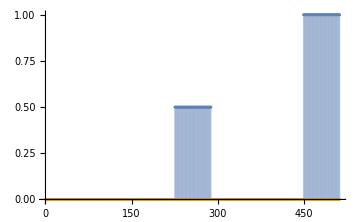
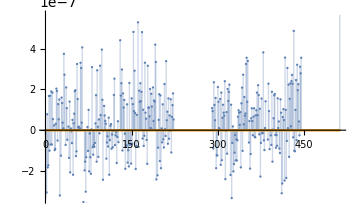

```mathematica
TF=ImportComplex["TransferF.dat"];
TFR=ImportComplex["TransferFReal.dat"];
{ListPlot[{Re@TF,Im@TF}/(2n-1),PlotRange->Automatic, Filling->Axis,ImageSize->Medium],
ListPlot[{Re@TFR,Im@TFR}/(2n-1),PlotRange->Automatic, Filling->Axis,ImageSize->Medium]}
```

Skąd aż taka różnica?
Patrząc poniżej wygląda na to, że KISS FTT robi jakiś trik wykonując odwrotną FTT

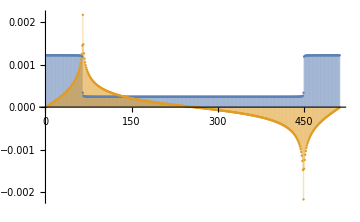
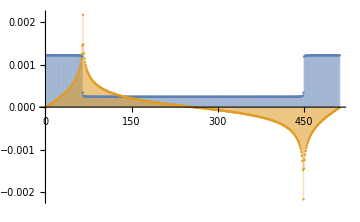

```mathematica
fp={1,-1};
{ListPlot[{Re@InverseFourier[coefs/(2n-1), FourierParameters->fp],Im@InverseFourier[coefs/(2n-1), FourierParameters->fp]},PlotRange->Full,ImageSize->Medium, Filling->Axis],
ListPlot[{Re@InverseFourier[coefsReal/(2n-1), FourierParameters->fp],Im@InverseFourier[coefsReal/(2n-1), FourierParameters->fp]},PlotRange->Full,ImageSize->Medium, Filling->Axis]}
```

## Filtry różnej długości

```mathematica
NicePrint[n_]:=Module[{f,TF,TF2,Org,Mag,Mag2},
f=Import["filtr"<>ToString[n]<>".dat","Data"];
TF=f[[All,2]]+ⅈ f[[All,3]];
TF2=f[[All,4]]+ⅈ f[[All,5]];
Org=f[[All,1]];
Mag=f[[All,6]];
Mag2=f[[All,7]];
{ListPlot[Org,PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListPlot[{Re@TF,Im@TF}/(n),PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListPlot[Abs[TF]/(n),PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListPlot[{Re@TF2,Im@TF2}/(n),PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListPlot[Abs[TF2]/(n),PlotRange->Full, Filling->Axis,ImageSize->Medium],
ListLogPlot[{Mag,Mag2}/(n),PlotRange->Full, Filling->Axis,ImageSize->Medium]
}
];
```

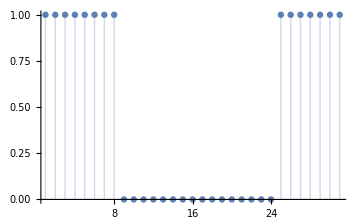
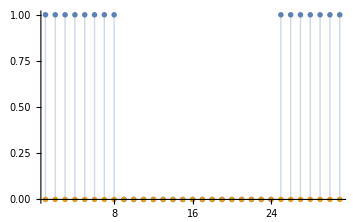
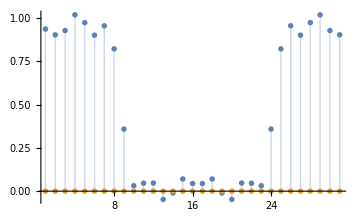
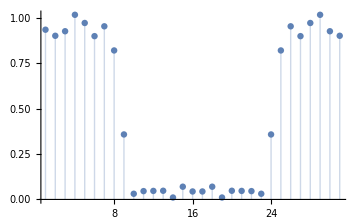
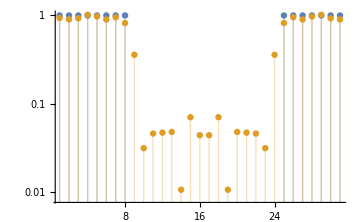
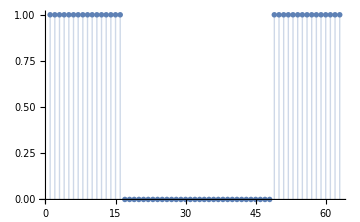
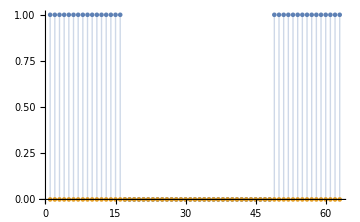
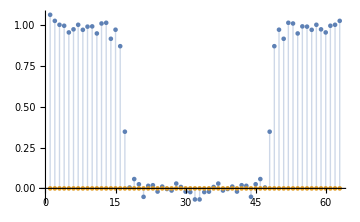
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
NicePrint[#]&/@{31,63,127,255,511,1023}
```

```mathematica
Nice2Print[list_,which_:4]:=Module[{Mag},
Mag=({#[[1]],Abs@#[[2]]}&/@(Import["filtr"<>ToString[#]<>".dat","Data"][[All,{8,which}]])ᵀ{1/(#-1),1/(#)})ᵀ&/@list;
ListLinePlot[Mag,PlotRange->Full,PlotLegends->list, Filling->Axis,ImageSize->Large]
];
```

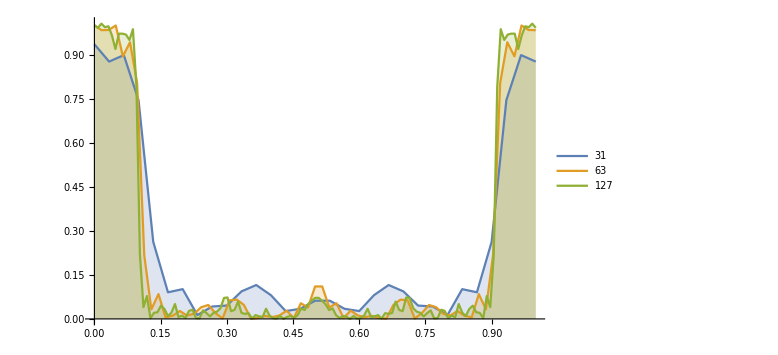

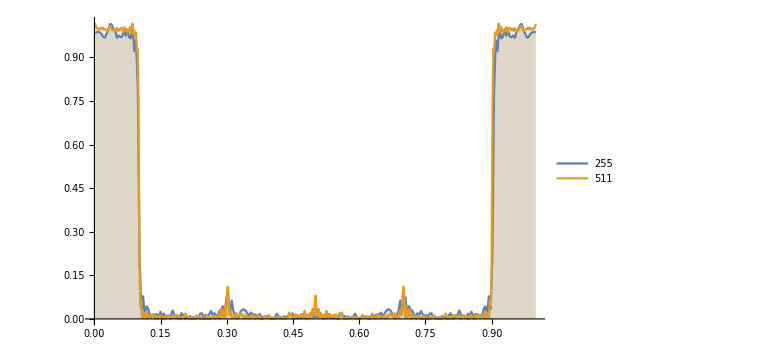

```mathematica
Nice2Print[{31,63,127}]
Nice2Print[{255,511}]
```

```mathematica
(({{3,2},{4,5}}ᵀ){3,1})ᵀ
```

{{9,2},{12,5}}

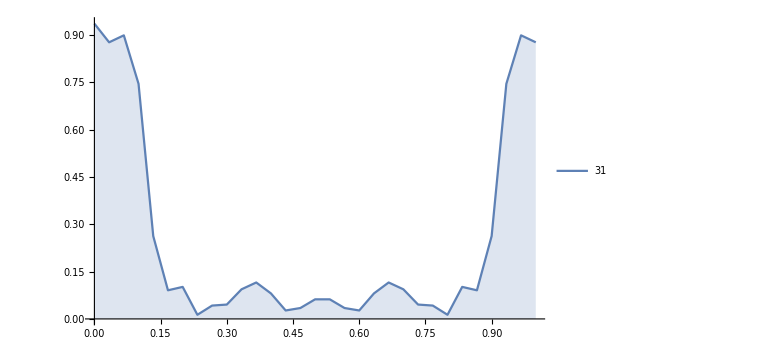

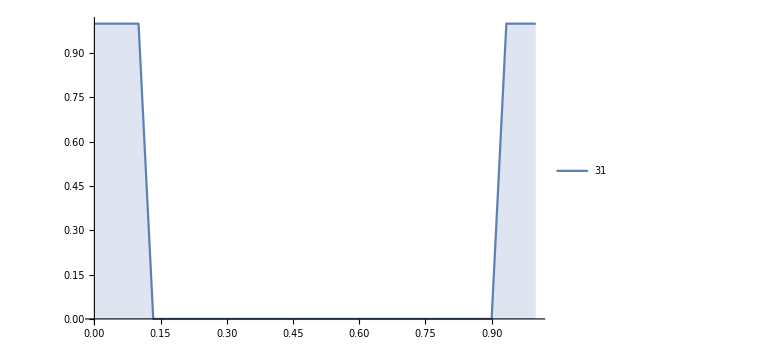

```mathematica
Nice2Print[{31}]
Nice2Print[{31},2]
```

### Stromość

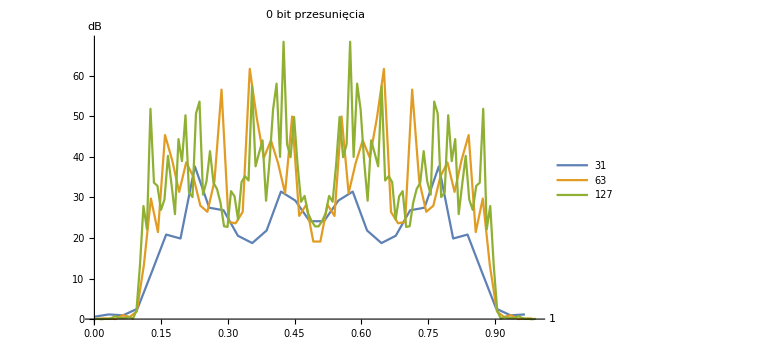

```mathematica
list={31,63,127};
alldata=((Import["filtr"<>ToString[#]<>".dat","Data"][[All,{8,4}]])ᵀ{1/#,1/#})ᵀ&/@list;
plotData=Map[{#[[1]],-20Log10@Abs@#[[2]]}&,alldata,{2}];ListLinePlot[plotData,PlotLegends->list,ImageSize->Large,PlotRange->Full,AxesLabel->{"1","dB"},PlotLabel->"0 bit przesunięcia"]
```

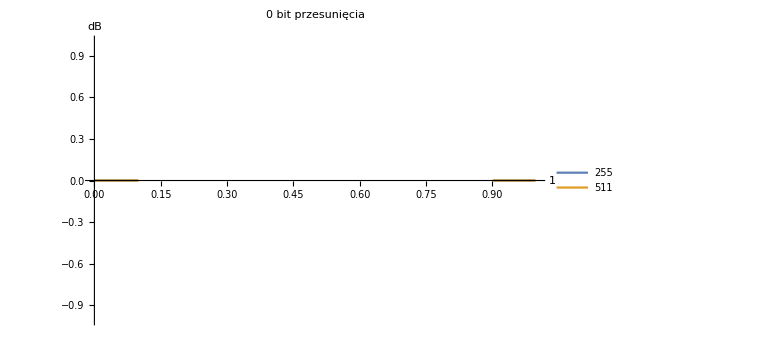

```mathematica
list={255,511};
alldata=((Import["filtr"<>ToString[#]<>".dat","Data"][[All,{8,2}]])ᵀ{1/#,1/#})ᵀ&/@list;
plotData=Map[{#[[1]],-20 Log10@Abs@#[[2]]}&,alldata,{2}];ListLinePlot[plotData,PlotRange->Full,PlotLegends->list,ImageSize->Large,AxesLabel->{"1","dB"},PlotLabel->"0 bit przesunięcia"]
```

{{{2,0.954593},{3,0.85841},{4,0.118949}},{{5,0.939446},{6,0.872952},{7,0.0831401}},{{11,0.977283},{12,0.914543},{13,0.127091}},{{24,0.964488},{25,0.906855},{26,0.0959914}},{{50,0.965813},{51,0.878736},{52,0.0993072}},{{101,0.957496},{102,0.864909},{103,0.0786565}}}

{{{1.,0.929409},{1.58496,3.05347},{2.,42.5812}},{{2.32193,1.24929},{2.58496,2.71748},{2.80735,49.7446}},{{3.45943,0.459572},{3.58496,1.78661},{3.70044,41.257}},{{4.58496,0.723149},{4.64386,1.95546},{4.70044,46.8699}},{{5.64386,0.6957},{5.67243,2.5854},{5.70044,46.1907}},{{6.65821,0.868675},{6.67243,2.90263},{6.6865,50.8533}}}

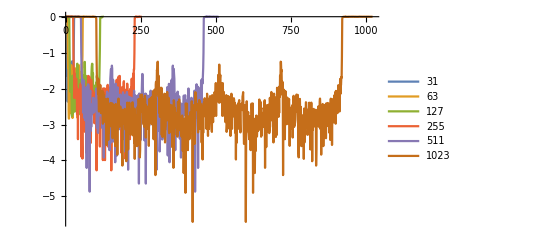

{{{0.584963,2.12406},{0.415037,39.5277}},{{0.263034,1.46819},{0.222392,47.0271}},{{0.125531,1.32704},{0.115477,39.4704}},{{0.0588937,1.23231},{0.0565835,44.9145}},{{0.0285692,1.8897},{0.0280144,43.6053}},{{0.0142139,2.03395},{0.0140752,47.9507}}}

{{3.63111,5.58174,10.5714,20.9243,66.1449,143.096},{95.2389,211.46,341.802,793.773,1556.53,3406.75}}

{{{31,3.63111},{63,5.58174},{127,10.5714},{255,20.9243},{511,66.1449},{1023,143.096}},{{31,95.2389},{63,211.46},{127,341.802},{255,793.773},{511,1556.53},{1023,3406.75}}}

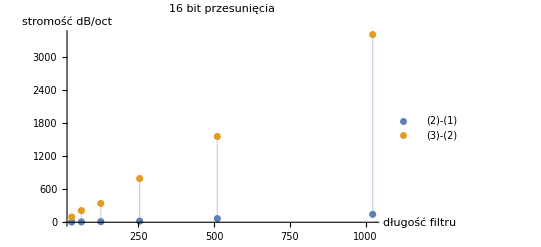

```mathematica
list={31,63,127,255,511,1023};
(*list={31};*)
alldata=((Import["filtr"<>ToString[#]<>".dat","Data"][[All,{8,4}]])ᵀ{1,1/#})ᵀ&/@list;
data=((Import["filtr"<>ToString[#]<>".dat","Data"][[All,{8,4}]])ᵀ{1,1/#})[[All,Floor[#/10];;Floor[#/10]+2]]ᵀ&/@list
logData=Map[{N@Log2@#[[1]],-20Log[Abs[#[[2]]]]}&,data,{2}]
plotData=Map[{#[[1]],Log10@Abs@#[[2]]}&,alldata,{2}];
ListLinePlot[plotData,PlotLegends->list]
difData=(Differences/@logData)
divData=Map[(#[[2]]/#[[1]])&,difData,{2}]ᵀ
final={list,#}ᵀ&/@divData
ListPlot[final,PlotLegends->{"(2)-(1)","(3)-(2)"},AxesLabel->{"długość filtru","stromość dB/oct"},PlotLabel->"16 bit przesunięcia", PlotRange->Full,Filling->{1->{2}}]
```

```mathematica
NicePrint[n_,which_:2]:=Module[{f,TF,TF2,Org,Mag,Mag2},
f=Import["filtr"<>ToString[n]<>".dat","Data"];
TF=f[[All,which]]+ⅈ f[[All,which+1]];

ListLinePlot[{ (TF),Arg@(TF/n)},PlotRange->Full, Filling->Axis,ImageSize->Large, PlotLegends->{"Wartości współczynników", "Faza"}]

];
```

```mathematica
NicePrint[
```

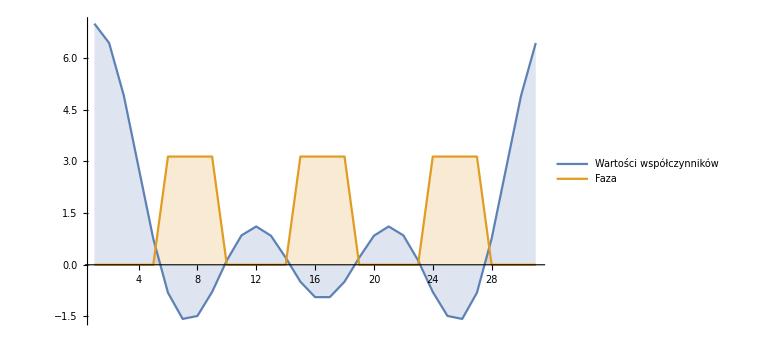

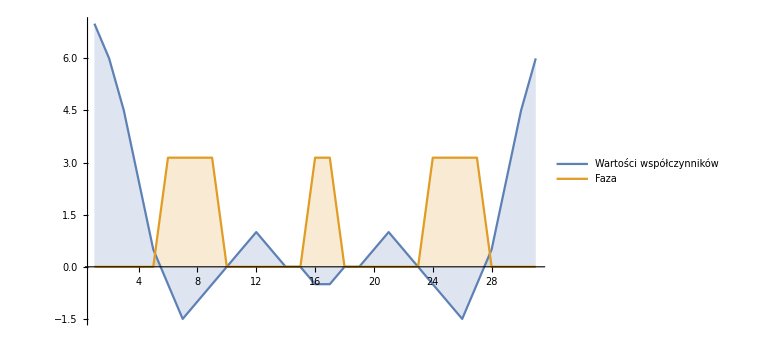

```mathematica
NicePrint[31,9]
NicePrint[31,11]
```

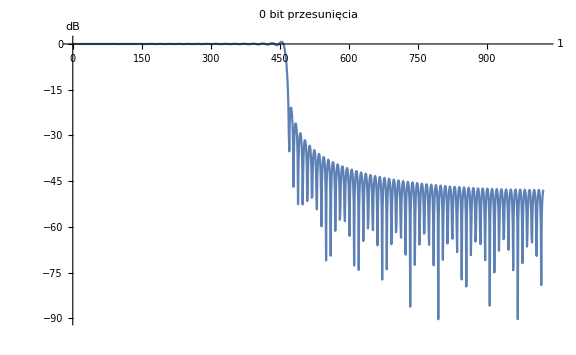

```mathematica
alldata=Import["lpf.dat","Data"][[All,{1,4}]];
ListLinePlot[alldata,PlotLegends->list,ImageSize->Large,PlotRange->Full,AxesLabel->{"1","dB"},PlotLabel->"0 bit przesunięcia"]
```

## Nowe testy

### Współczynniki → transmitancja

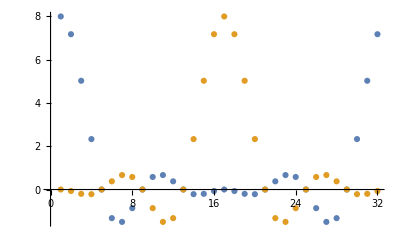

```mathematica
ListPlot[{coefs,RotateRight[coefs,nn/2]}]
```

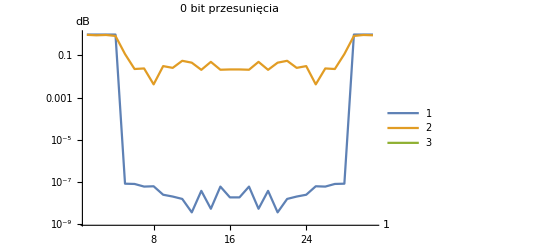

```mathematica
nn=32;
coefs= Import["filtr"<>ToString[nn-1]<>".dat","Data"][[All,9]];
coefs2= Import["filtr"<>ToString[nn-1]<>".dat","Data"][[All,11]];
transmitance=Abs@Fourier[coefs/nn,FourierParameters->{1, -1}];
transmitance2=Abs@Fourier[coefs2/nn,FourierParameters->{1, -1}];
rotCoefs=RotateRight[coefs,nn/2];
rotTransmitance=0.Fourier[rotCoefs/nn,FourierParameters->{1, -1}];
ListLogPlot[{transmitance,transmitance2,rotTransmitance},PlotLegends->Automatic,PlotRange->Full,AxesLabel->{"1","dB"},PlotLabel->"0 bit przesunięcia",ImageSize->Full,Joined->True]
```

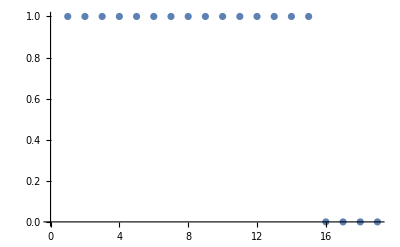

```mathematica
ListPlot@Abs@Chop@InverseFourier[RotateLeft[Fourier[{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0}],20]]
```

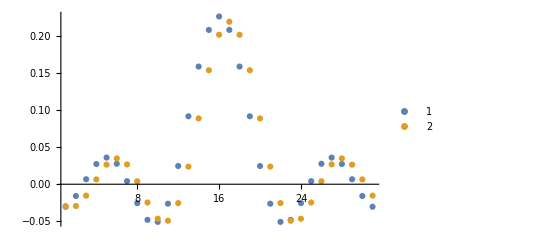

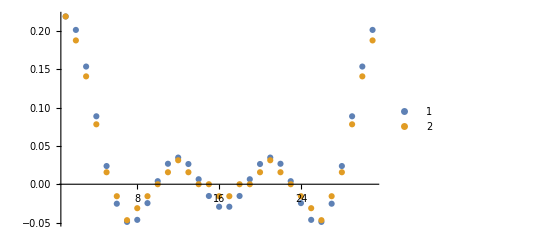

```mathematica
freq=Table[UnitStep[-x+0.2],{x,0,1-2/nn,2/nn}];
ListPlot[{FrequencySamplingFilterKernel[freq],rotCoefs/nn},PlotRange->Full,PlotLegends->Automatic]
ListPlot[{coefs/nn,coefs2/nn},PlotRange->Full,PlotLegends->Automatic]
```

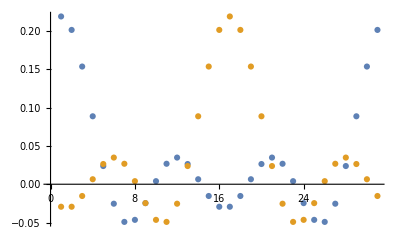

```mathematica
ListPlot[{coefs/nn,rotCoefs/nn}]
```

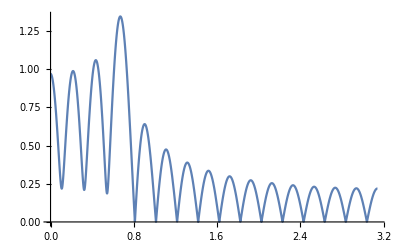

```mathematica
Plot[Abs[ListFourierSequenceTransform[PadLeft[coefs,Length@coefs+20]/nn,x]],{x,0,π},PlotRange->All, Exclusions->False]
```

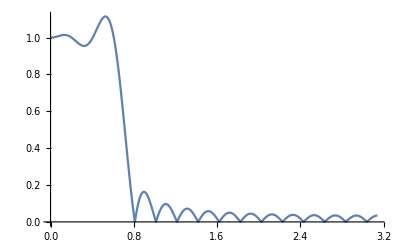

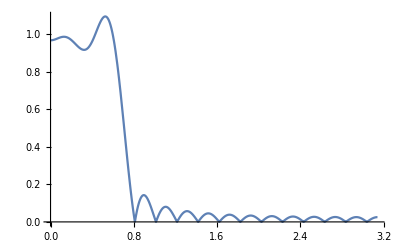

```mathematica
Plot[Abs[ListFourierSequenceTransform[FrequencySamplingFilterKernel[freq],x]],{x,0,π},PlotRange->All, Exclusions->False]
Plot[Abs[ListFourierSequenceTransform[rotCoefs/nn,x]],{x,0,π},PlotRange->All, Exclusions->False]
```

```mathematica
co={1,1,1,1,0,0,0,0};
Table[Plot[Im[Sum[(RotateRight[co,j][[i]]/nn )Exp[-ⅈ(i)x],{i,Length[co]}]],{x,0,π},PlotRange->All, Exclusions->False],{j,0,nn/2}]
```

Table[Plot[Im[∑_i^Length[co] (RotateRight[co,j]⟦i⟧ Exp[-ⅈ i x])/nn],{x,0,π},PlotRange→All,Exclusions→False],{j,0,{16,32,64,128,256,512}}]

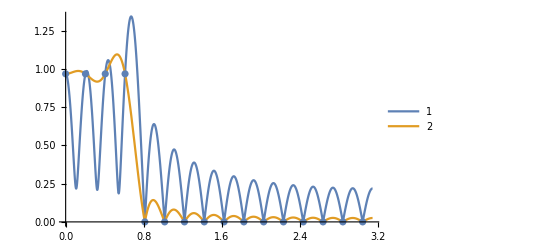

```mathematica
args=Table[i,{i,0,π(1-(1/(nn-1))),2π/(nn-1)}];
Length@args;
Length@coefs;
Show[Plot[{Abs[ListFourierSequenceTransform[coefs,x]]/(nn),Abs[ListFourierSequenceTransform[rotCoefs,x]]/(nn)},{x,0,π},PlotRange->All,PlotLegends->Automatic],
ListPlot[{args,transmitance[[1;;nn/2]]}ᵀ]]
```

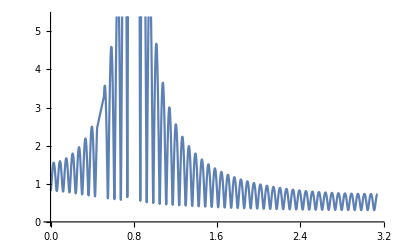

```mathematica
sinus=Table[Sin[2π 0.8(16/π) x],{x,0,π,1/32}];
Plot[Abs@ListFourierSequenceTransform[sinus,x],{x,0,π}]
```

```mathematica
a=Manipulate[
sin=Table[Sin[1. 2π f x],{x,0,π /f,1/(fp)}];
Grid[{{
ListLinePlot[{sin,
ListConvolve[coefs,sin]/Length@coefs,
ListConvolve[rotCoefs,sin]/Length@rotCoefs},
ImageSize->Large,PlotStyle->{Black,Blue,Red},AxesLabel->{"t (up to π/f)",""} ,PlotLegends->{"f: "<>ToString[f]<>"Hz\nfp: " <>ToString[fp]<>"Hz","coefs","rotCoefs"}],
Plot[{Abs[ListFourierSequenceTransform[coefs,x]]/(nn),Abs[ListFourierSequenceTransform[rotCoefs,x]]/(nn)},{x,0,π}, PlotStyle->{Blue,Red},PlotRange->All,ImageSize->Large,Epilog->Line[{{2π f/(fp),0},{2π f/(fp),2}}],PlotLegends->{"coefs","rotCoefs"}]
}}],{{f,1},1,fp/2},{{fp,30},10,1000},AutorunSequencing->{{1,20}}]
```

```mathematica
Export["anim.mov",a,Antialiasing->True,"VideoEncoding"->"Apple Intermediate Codec"]
```

$Aborted

```mathematica
a=Module[{sin,fp,f},
fp=30;
sin=Table[Sin[1. 2π f x],{x,0,π /f,1/(fp)}];
Table[Grid[{{
ListLinePlot[{sin,
ListConvolve[coefs,sin,1]/Length@coefs,
ListConvolve[rotCoefs,sin,1]/Length@rotCoefs},
ImageSize->Large,PlotRange->{Automatic,{-1.1,1.1}},PlotStyle->{Black,Blue,Red},AxesLabel->{"t (up to π/f)",""} ,PlotLegends->{"f: "<>ToString[f]<>"Hz\nfp: " <>ToString[fp]<>"Hz","coefs","rotCoefs"}],
Plot[{Abs[ListFourierSequenceTransform[coefs,x]]/(nn),Abs[ListFourierSequenceTransform[rotCoefs,x]]/(nn)},{x,0,π}, PlotStyle->{Blue,Red},PlotRange->All,ImageSize->Large,Epilog->Line[{{2π f/(fp),0},{2π f/(fp),2}}],PlotLegends->{"coefs","rotCoefs"}]
}}],{f,1,fp/2,0.1}]];
```

```mathematica
Export["filtr.gif",a]
```

filtr.gif

```mathematica
CloudDeploy[%]
```

CloudObject[]

### Sygnał

```mathematica
Fun[x_]:=Sum[Cos[x 2.π(55+( i/(1000 nn)))],{i,0,nn-1}]/nn;
signal=Table[Fun[x],{x,0,1,1/(nn-2)}];
Length@signal;
```

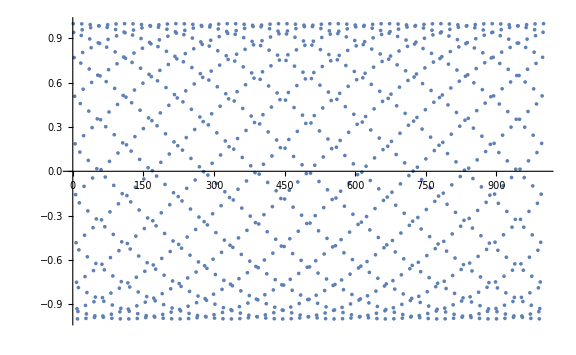

```mathematica
ListPlot[signal,ImageSize->Large,PlotRange->Full]
```

### Spektrum sygnału

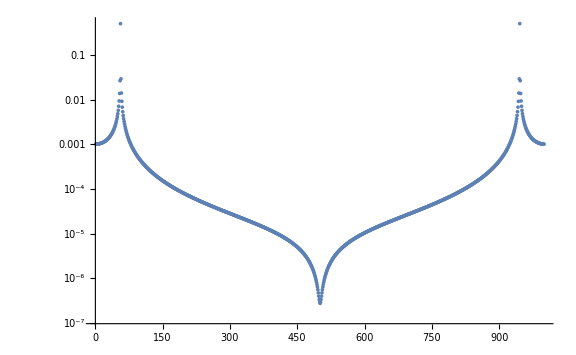

```mathematica
Fsignal=Fourier[signal/Length@signal,FourierParameters->{1, -1}];
ListLogPlot[Abs@Fsignal[[1;;nn-1]],ImageSize->Large, PlotRange->Full]
```

### H(ω)X(ω)

```mathematica
ListLogPlot[{
transmitance,Abs[Fsignal][[1;;nn-1]],transmitance*(Abs@Fsignal[[1;;(nn-1)]])},
PlotRange->All,ImageSize->Full,PlotLegends->{"transmitancja","spektrum","iloczyn"}]
```

### F[h[t]] F[x[t]]

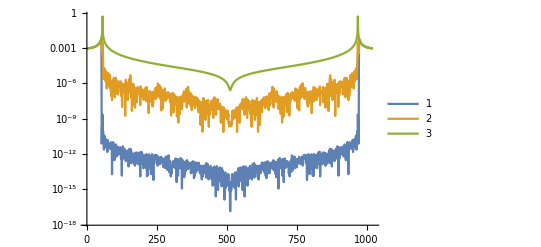

```mathematica
ListLogPlot[{Abs[Fourier[coefs/Length@coefs,FourierParameters->{1, -1}]Fourier[signal/Length@signal,FourierParameters->{1, -1}][[1;;(nn-1)]]][[1;;nn-1]],
Abs[Fourier[coefs2/Length@coefs2,FourierParameters->{1, -1}]Fourier[signal/Length@signal,FourierParameters->{1, -1}][[1;;(nn-1)]]][[1;;nn-1]],
Abs@Fsignal[[1;;nn-1]]},PlotRange->Full,ImageSize->Full,Joined->True, PlotLegends->Automatic]
```

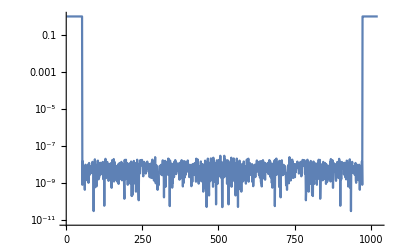

```mathematica
ListLogPlot[Abs[Fourier[coefs/Length@coefs,FourierParameters->{1, -1}]Fourier[signal/Length@signal,FourierParameters->{1, -1}][[1;;(nn-1)]]][[1;;nn-1]]/Abs@Fsignal[[1;;nn-1]],PlotRange->Full,ImageSize->Full, Joined->True]
```

decymacja
- odtwórz charakterystykę
- dla low pass i high pass
zrób macierz obcięcia x długość współczynników

```mathematica
dwa=ListLinePlot[Chop@InverseFourier[Fourier[coefs/Length@coefs,FourierParameters->{1, -1}]Fourier[signal/Length@signal,FourierParameters->{1, -1}][[1;;(nn-1)]]],PlotRange->Full,ImageSize->Full]
```

### Konwolucja x[t]*h[t]

```mathematica
ListPlot[{(Chop@InverseFourier[Fourier[coefs/Length@coefs,FourierParameters->{1, -1}]Fourier[signal/Length@signal,FourierParameters->{1, -1}][[1;;(nn-1)]]])/splot},PlotRange->Automatic]
```

-Graphics-

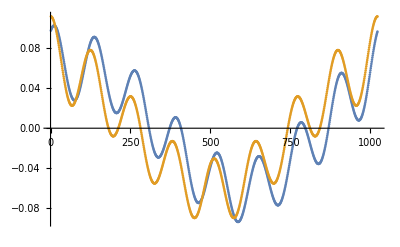

```mathematica
ListPlot[{(Chop@InverseFourier[Fourier[coefs/Length@coefs,FourierParameters->{1, -1}]Fourier[signal/Length@signal,FourierParameters->{1, -1}][[1;;(nn-1)]]]),splot/√1023},PlotRange->Full,ImageSize->Full]
```

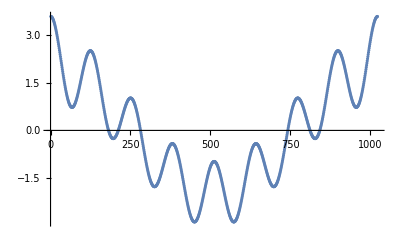

```mathematica
splot=ListConvolve[signal,coefs/Length@coefs,{1,1}];
raz=ListPlot[splot,PlotRange->Full,ImageSize->Full]
```

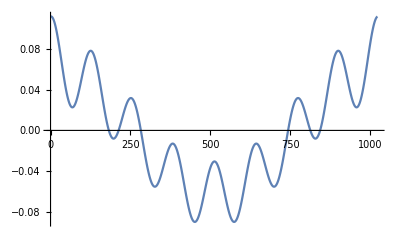
Show[-Graphics-/-Graphics-]

```mathematica
Show[raz/dwa]
```

### F[x[t]*h[t]]

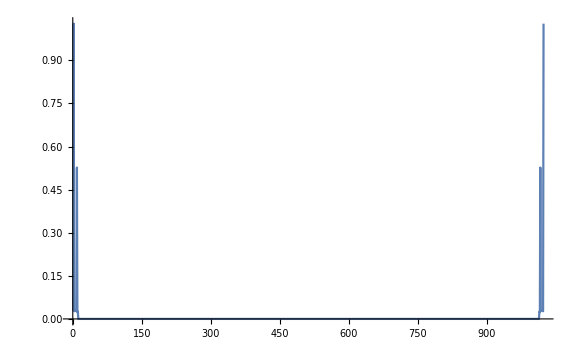

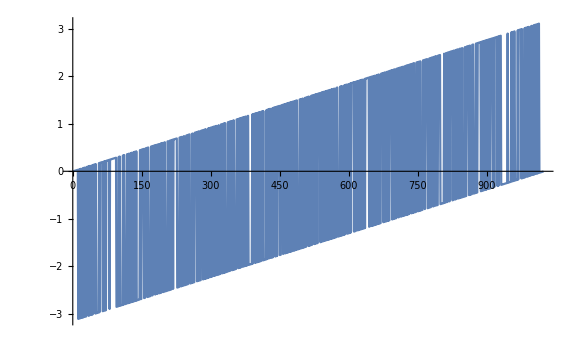

```mathematica
Fsplot=Fourier[splot/Length@splot,FourierParameters->{1, -1}];
ListLinePlot[Abs@Fsplot[[1;;nn-1]],PlotRange->Full,ImageSize->Large]
ListLinePlot[Arg@Fsplot[[1;;nn-1]],PlotRange->Full,ImageSize->Large]
```

```mathematica
ListConvolve[{c,d,e,f,g,h},{x,y},{1,1}]
```

{c x+e x+g x+d y+f y+h y,d x+f x+h x+c y+e y+g y}

## Sanity check

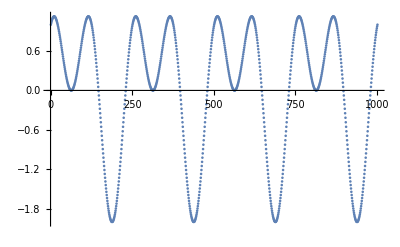

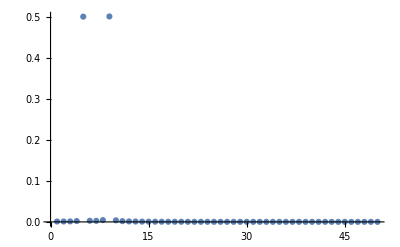

```mathematica
sin=Table[Sin[2π 4  x]+Cos[2π 8 x],{x,0,1,0.001}];
nn=Length@sin;
ListPlot@sin
ListPlot[(Abs@Fourier[sin,FourierParameters->{1, -1}]/nn)[[1;;50]],PlotRange->All]
```

### Convolution[] = invF[F[]F[]]

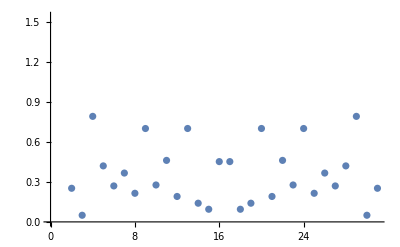

-Graphics-

```mathematica
{a, b} = RandomReal[1, {2,31}];
ListPlot[Abs[Fourier[ListConvolve[a, b, 1]] ]]
ListPlot[Abs[Fourier[a] Fourier[b] Sqrt[31]]]
```

```mathematica
FullSimplify[Sum[Sin[i x],{i,0,n}]]/.{n->10}
```

Csc[x/2] Sin[5 x] Sin[(11 x)/2]

```mathematica
Sin[x/2]Sin[n x/2]/Sin[x(n+1)/2]/.{n->10}
```

Csc[(11 x)/2] Sin[x/2] Sin[5 x]

```mathematica
Sum[Sin[i x],{i,0,2}]
```

Sin[x]+Sin[2 x]

## Mathematica filters

### Frequency sampling

```mathematica
a=FrequencySamplingFilterKernel[{1,1,1,1,0,0,0,0}]
```

{-0.0498159,0.0412023,0.0666667,-0.0364879,-0.107869,0.034078,0.318892,0.466667,0.318892,0.034078,-0.107869,-0.0364879,0.0666667,0.0412023,-0.0498159}

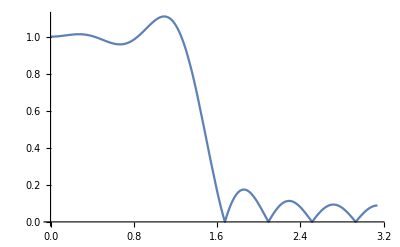

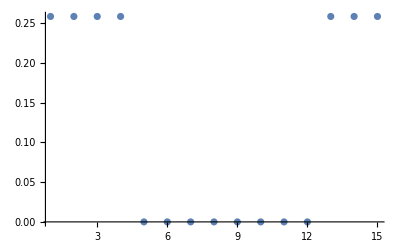

```mathematica
Plot[Abs[ListFourierSequenceTransform[a,x]],{x,0,π},PlotRange->All]
ListPlot[Abs[Fourier[a]],PlotRange->All]
```

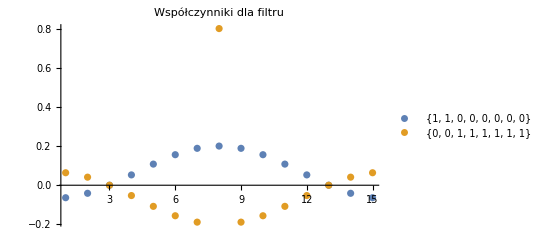

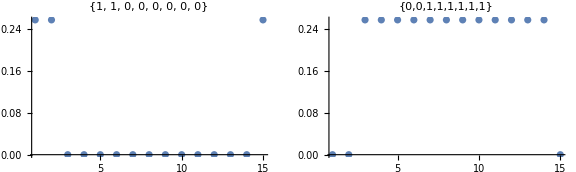

```mathematica
first={1,1,0,0,0,0,0,0};
second={0,0,1,1,1,1,1,1};
ListPlot[{FrequencySamplingFilterKernel[first],FrequencySamplingFilterKernel[second]},PlotRange->Full,PlotLegends->{ToString@first,ToString@second},PlotLabel->"Współczynniki dla filtru"]
GraphicsRow[{ListPlot[Abs[Fourier[RotateRight[FrequencySamplingFilterKernel[first]]]],PlotRange->All,PlotLabel->ToString@first],
ListPlot[Abs[Fourier[FrequencySamplingFilterKernel[second]]],PlotLabel->second,PlotRange->All]},ImageSize->Large]
```

Filtry po odtworzeniu ze współczynników:

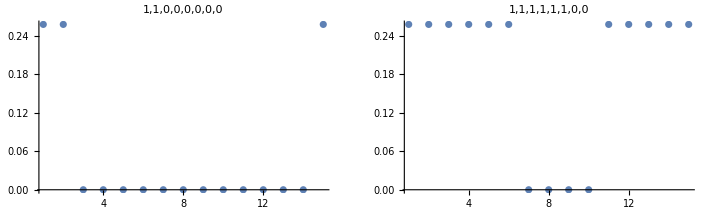

{0.069411,-0.0540319,-0.10942,0.0473735,0.319394,0.454545,0.319394,0.0473735,-0.10942,-0.0540319,0.069411}

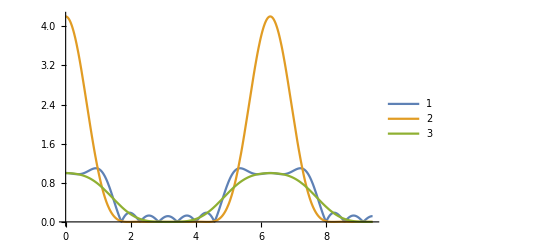

```mathematica
fir=FrequencySamplingFilterKernel[{1,1,1,0,0,0}]
win=Array[BlackmanWindow,Length[fir],{-1/2,1/2}];
Plot[Evaluate[Abs[ListFourierSequenceTransform[#,x]]&/@{fir,win, win fir}],{x,0,3π},PlotLegends->Automatic,PlotRange->Full]
```

{0.0292362,0.055524,-0.026334,-0.0655035,-0.0466696,0.106116,0.293767,0.382398,0.293767,0.106116,-0.0466696,-0.0655035,-0.026334,0.055524,0.0292362}

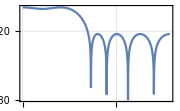

```mathematica
a=EquirippleFilterKernel[{{{0,1},{1.4,Pi}},{1, 0}},15]
BodePlot[ListZTransform[a,z],{0,π},SamplingPeriod->1,PlotLayout->"Magnitude",ScalingFunctions->{"Linear",Automatic},GridLines->Automatic,ImageSize->Small]
```